# Axon Image Analyzing

Analysis of axon expression intensity in the neocortex

Jihyeon Je, Jun. 29,  2018

Axon, also known as the nerve fiber, is a long, slender projection of a nerve cell, or neuron, that conducts electrical impulses known as action potentials, away from the nerve cell body. Although the connectivity of axons are crucial in signal transfer between neurons, its structural assembly and trend across the cortex is yet not widely investigated. By utilizing image processing techniques, we look at the structural trend and are able to quantify axon expressions, providing valuable data for further investigation of neuronal activity.

## Background

```mathematica
{Import ["Desktop/55800_cortex_md.gif"], Import["Desktop/neuron.png"]}
```

{-Graphics-,{-Graphics-}}

The neocortex, also called the neopallium and isocortex, is the part of the mammalian brain involved in higher-order brain functions such as sensory perception, cognition, generation of motor commands, spatial reasoning and language. The neocortex is the largest part of the cerebral cortex -  outer layer of the cerebrum - in human brain.

The neocortex is made up of six layers, labelled from the outermost inwards, I to VI. Since different layers specialize in different activities, analysis of changing trend in axon density across the layers is crucial to understanding brain activity. Plasticity over longer distances means that a larger number of neural circuits can be achieved and implies a larger memory capacity per synapse (Fawcett and Geller, 1998, Chen et al., 2002, Papadopoulos, 2002).

Axons span many millimeters of cortical territory, and individual axons target diverse areas (Zhang and Deschenes, 1998). Thus, understanding the repertoire of axonal structural changes is fundamental to evaluating mechanisms of functional rewiring in the brain.

Images acquired from distinct axon arbors in adult barrel cortex of GFP transgenic mice were used in this project. Two-photon microscopy techniques were used along with SBEM(Serial Block-face scanning Electron Microscopy) techniques. Images were obtained after a series of surface scanning throughout the entire sample, then stacked for segmentation and quantification. Due to the size of the data, only the first section of layer 1 was analyzed in this project.

## Import Images

In order to carry out an image analysis with electron-microscope images, image data (real-value pixel sizes corresponding to each pixels) is needed.

#### Input Pixel Sizes

Assign pixel sizes:

```mathematica
xpixelsize = 512 Quantity[, "Micrometers"];
ypixelsize = 512 Quantity[, "Micrometers"];
zstepsize = 293 Quantity[, "Micrometers"];
```

#### Import Image Stack

Import Tif stack from directory:

```mathematica
image = Import[FileNameJoin[{NotebookDirectory[],"axon.tif"}]];
```

## Image Processing

After images are imported, 3D mesh is created for visualization of general structural trend throughout the entire stack. Maximum intensity projection is also generated from the stacks to aid the understanding of overall axon distribution.

To carry out density and volume calculations, images were binarized with given thresholds.

#### 3D mesh

Create a 3D mesh with the image stack:

```mathematica
image3D=Image3D[image,ColorFunction->"GrayLevelOpacity",BoxRatios->{1,1,1/3}]
```

#### Binarization

Binarize images with set thresholds:

```mathematica
binarized = Map[MorphologicalBinarize[#, {0.10, 0.4}]&,ImageAdjust/@image];
```

#### Maximum Intensity Projection

Create maximum intensity projection from the previously created binarized images:

```mathematica
MIP = Image3DProjection[Image3D[binarized]]
```

-Graphics-

Display mesh and temporal interpolation side by side for convenient analysis:

```mathematica
{Labeled[image3D,Text@"3D mesh"],Labeled[MIP,Text@"Maximum Intensity Projection"]}
```

{-Graphics3D-3D mesh,-Graphics-Maximum Intensity Projection}

## Calculate Volume and Density

With processed images, we are now able to calculate volume and density of the axons expressed in the images.

#### Calculate volume

Volume of total axons expressed were calculated by counting all non-zero elements in the binarized images and multiplying them by pixel sizes.

Count number of non-zero elements in the binarized image, multiply it with pixel sizes:

```mathematica
expressedvol = Count[Flatten[ImageData /@ binarized],1]*xpixelsize*ypixelsize*zstepsize
```

12353445560320 µm^3

Calculate the volume of the entire image stack by counting image dimensions and multiplying it with pixel sizes:

```mathematica
totalvol = First[ImageDimensions[First[image]]]*xpixelsize*Last[ImageDimensions[First[image]]]*ypixelsize*Length[image]*zstepsize
```

1208088401018880 µm^3

Average axon volume:

```mathematica
denstiy = N[expressedvol/totalvol]Quantity[, "Micrometers"]
```

0.0102256 µm

By casting a sliding window across the entire image stack from top to bottom,  the general trend of axon density was observed. Since connectivity between axons is a crucial in understanding brain activity, sliding window allows an analysis of the amount of shared data between axons across the brain.

Cast a sliding window across image stack:

```mathematica
slidingwindow[x_] := Count[Flatten[ImageData[x]],1]
SetAttributes[slidingwindow,Listable];
window = Total /@ MovingMap[slidingwindow, binarized, 2];
```

Plot graph:

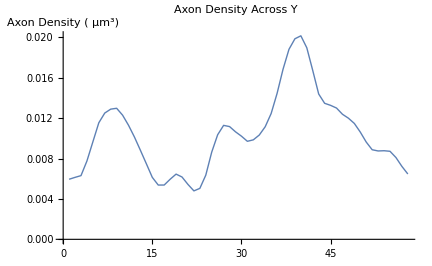

```mathematica
Show[ListPlot[window/(First[ImageDimensions[First[image]]]* Last[ImageDimensions[First[image]]]*3), Joined -> True, PlotStyle->Thick, PlotLabel-> "Axon Density Across Y",LabelStyle->Directive[Bold],  AxesLabel->"Axon Density ( µm^3)" ]]
```

## References

Image data acquired from Diadem Challenge - Neocortical Layer Axon 1 : http://www.diademchallenge.org/neocortical_layer_1_axons_readme.html

De Paola V1 et al. (2006) Cell type-specific structural plasticity of axonal branches and boutons in the adult neocortex. Cold Spring Harbor Symp. Quant. Neruon. 49, 861-875.

## Author contact information

Jihyeon Je

jej19@wra.net